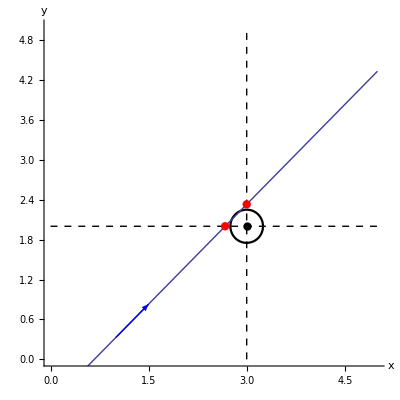

```mathematica
Show[ContourPlot[(x-3)^2+(y-2)^2==0.25^2,{x,0,5},{y,0,5},Frame->False,Axes->True,AspectRatio->1,AxesLabel->{"x","y"},ContourStyle->Directive[Thickness[0.004],Black],AxesStyle->Thickness[0.003],LabelStyle->Directive[FontFamily->"Courier",FontSize->18]],ListPlot[{{3,2}},PlotStyle->Directive[PointSize[0.015],Black]],ContourPlot[{x==3,y==2},{x,0,5},{y,0,5},ContourStyle->Dashed],Plot[x-0.67,{x,0,5}],Graphics[{Blue,Arrow[{{1,1-0.67},{1.5,1.5-0.67}}]}],ListPlot[{{2.67,2}},PlotStyle->Directive[PointSize[0.015],Red]],ListPlot[{{3,3-0.67}},PlotStyle->Directive[PointSize[0.015],Red]]]
```

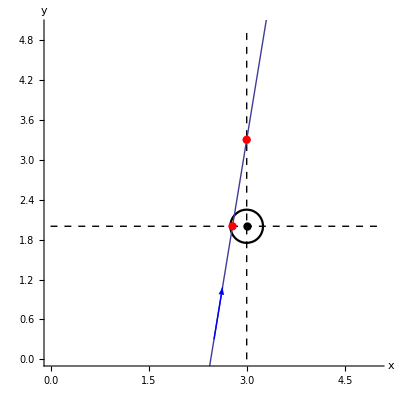

```mathematica
Show[ContourPlot[(x-3)^2+(y-2)^2==0.25^2,{x,0,5},{y,0,5},Frame->False,Axes->True,AspectRatio->1,AxesLabel->{"x","y"},ContourStyle->Directive[Thickness[0.004],Black],AxesStyle->Thickness[0.003],LabelStyle->Directive[FontFamily->"Courier",FontSize->18]],ListPlot[{{3,2}},PlotStyle->Directive[PointSize[0.015],Black]],ContourPlot[{x==3,y==2},{x,0,5},{y,0,5},ContourStyle->Dashed],Plot[6(x-2.45),{x,0,5}],Graphics[{Blue,Arrow[{{2.5,6*0.05},{2.63,6(2.63-2.45)}}]}],ListPlot[{{2.45+2/6,2}},PlotStyle->Directive[PointSize[0.015],Red]],ListPlot[{{3,6(3-2.45)}},PlotStyle->Directive[PointSize[0.015],Red]]]
```

```mathematica
(*******************************************)
```

```mathematica
isect[r_,k_,b_]:={x,y}/.Solve[{x^2+y^2==r^2,y==k x+b},{x,y}]
```

```mathematica
a:=Arrow[{{isect[3, 2, 3 √(1+4)-2][[1]][[1]]-0.5,isect[3, 2, 3 √(1+4)-2][[1]][[2]]-1},isect[3, 2, 3 √(1+4)-2][[1]]}]
```

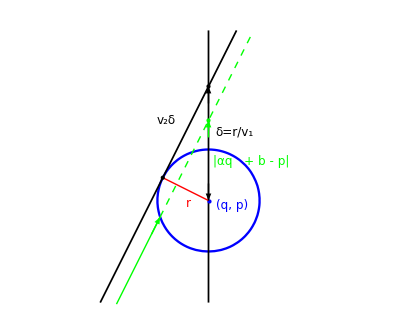

```mathematica
Show[ContourPlot[{x^2+y^2==3^2,x==0,y==2x+3 √(1+4)},{x,-10,10},{y,-6,10},AspectRatio->Automatic,Frame->False,ContourStyle->{Directive[Thickness[0.004],Blue],Directive[Thickness[0.003],Black],Directive[Thickness[0.003],Black]}],ListPlot[{{0,0}},PlotStyle->Directive[Blue,PointSize[Large]]],Graphics[{Green,a}],Graphics[{Red,Line[{{0,0},isect[3,2,3 √(1+4)][[1]]}]}],Graphics[{Green,Thick,Line[{{-5.4,2(-5.4)+3 √(1+4)-2},{-2.83895548663342,-0.9697070407674702}}]}],Graphics[{Green,Thick,Dashed,Line[{{-2.83895548663342,-0.9697070407674702},{2.6,2(2.6)+3 √(1+4)-2}}]}],Graphics[{Red,Text[Style["r",12,Italic],{-1.2,-0.2}]}],Graphics[{Green,Text[Style["|αq   + b - p|",12,Italic],{2.5,2.3}]}],Graphics[{Blue,Text[Style["(q, p)",12,Italic],{1.4,-0.3}]}],Graphics[{Black,Text[Style["v_2δ",12,Italic],{-2.5,4.7}]}],Graphics[{Black,Text[Style["δ=r/v_1",12,Italic],{1.5,4}]}],ListPlot[{{-6/(√5),3/(√5)}},PlotStyle->Directive[Black,PointSize[Medium]]],ListPlot[{{0,3 √5}},PlotStyle->Directive[Black,PointSize[Medium]]],ListPlot[{{0,3 √5-2}},PlotStyle->Directive[Green,PointSize[Medium]]],Graphics[{Black,Arrow[{{0,1},{0,0}}]}],Graphics[{Black,Arrow[{{0,3 √5-1},{0,3 √5}}]}],Graphics[{Green,Arrow[{{0,3 √5-3},{0,3 √5-2}}]}]]
```

```mathematica
,Graphics[{Black,Text[Style["}",80],{1.1,2.7}]}]
```

```mathematica
isect[3, 2, 3 √(1+4)]
```

{{-6/(√5),3/(√5)},{-6/(√5),3/(√5)}}

```mathematica
isect[3, 2, 3 √(1+4)-2][[1]]//N
```

{-2.83896,-0.969707}

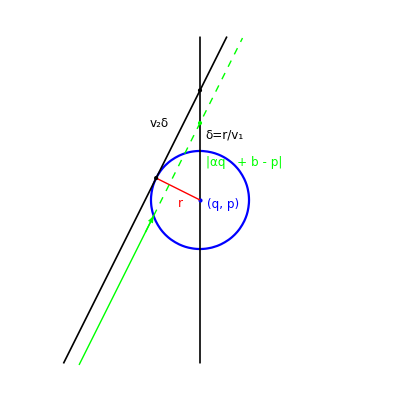

```mathematica
Show[ContourPlot[{x^2+y^2==3^2,x==0,y==2x+3 √(1+4)},{x,-10,10},{y,-10,10},AspectRatio->Automatic,Frame->False,ContourStyle->{Directive[Thickness[0.004],Blue],Directive[Thickness[0.003],Black],Directive[Thickness[0.003],Black]}],ListPlot[{{0,0}},PlotStyle->Directive[Blue,PointSize[Large]]],Graphics[{Green,a}],Graphics[{Red,Line[{{0,0},isect[3,2,3 √(1+4)][[1]]}]}],Graphics[{Green,Thick,Line[{{-7.4,2(-7.4)+3 √(1+4)-2},{-2.83895548663342,-0.9697070407674702}}]}],Graphics[{Green,Thick,Dashed,Line[{{-2.83895548663342,-0.9697070407674702},{2.6,2(2.6)+3 √(1+4)-2}}]}],Graphics[{Red,Text[Style["r",12,Italic],{-1.2,-0.2}]}],Graphics[{Green,Text[Style["|αq   + b - p|",12,Italic],{2.7,2.3}]}],Graphics[{Blue,Text[Style["(q, p)",12,Italic],{1.4,-0.3}]}],Graphics[{Black,Text[Style["v_2δ",12,Italic],{-2.5,4.7}]}],Graphics[{Black,Text[Style["δ=r/v_1",12,Italic],{1.5,4}]}],ListPlot[{{-6/(√5),3/(√5)}},PlotStyle->Directive[Black,PointSize[Medium]]],ListPlot[{{0,3 √5}},PlotStyle->Directive[Black,PointSize[Medium]]],ListPlot[{{0,3 √5-2}},PlotStyle->Directive[Green,PointSize[Medium]]]]
```